```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/c++/seminar"];
```

```mathematica
Oscillator=Import["oscillator.dat"];
```

```mathematica
xList=Oscillator.{{1,0},{0,1},{0,0}};
```

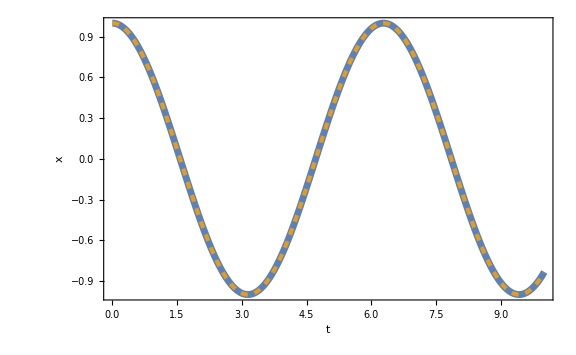

```mathematica
Show[ListPlot[xList,FrameLabel->{t,x},PlotLegends->Placed[LineLegend[{"num"},LegendMarkerSize->30],{0.87,0.8}],PlotStyle->AbsoluteThickness[5]],Plot[Cos[t],{t,0,10},PlotStyle->{Color[2],Dashed,AbsoluteThickness[3]},PlotLegends->Placed[LineLegend[{"cos t"},LegendMarkerSize->30],{0.87,0.8}]]]
```

```mathematica
Osc2=Import["2oscillator.dat"];
```

```mathematica
xList=Osc2.{{1,0},{0,1},{0,0},{0,0},{0,0}};
yList=Osc2.{{1,0},{0,0},{0,0},{0,1},{0,0}};
```

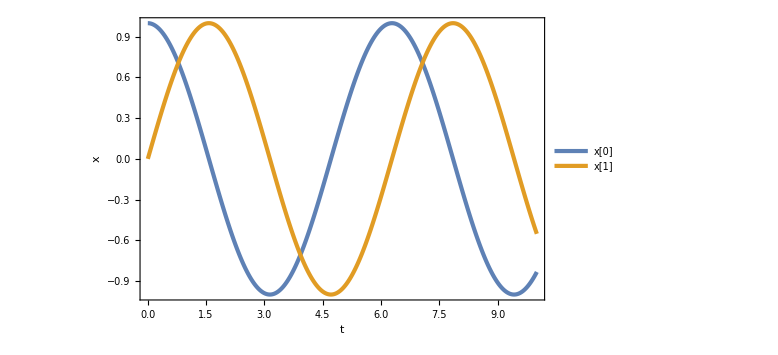

```mathematica
ListPlot[{xList,yList},FrameLabel->{t,x},PlotLegends->Placed[{"x[0]","x[1]"},{0.1,0.2}]]
```

```mathematica
DCbg=Import["double_chaotic_bg.dat"];
```

```mathematica
phiList=Map[{#[[6]],#[[2]]}&,DCbg];
psiList=Map[{#[[6]],#[[4]]}&,DCbg];
HList=Map[{#[[6]],#[[7]]}&,DCbg];
eList=Map[{#[[6]],#[[8]]}&,DCbg];
```

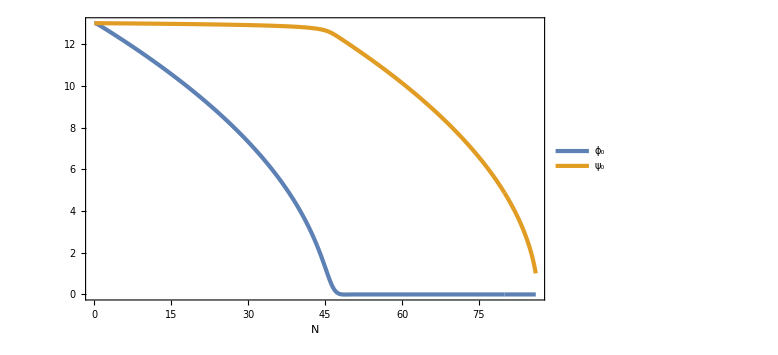

```mathematica
ListPlot[{phiList,psiList},FrameLabel->{N,None},PlotLegends->Placed[{Subscript[ϕ, 0],Subscript[ψ, 0]},{0.2,0.2}]]
```

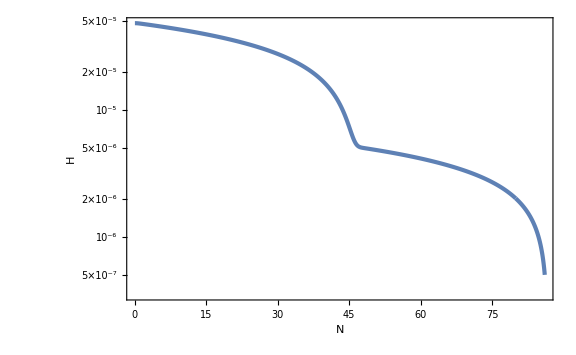

```mathematica
ListLogPlot[HList,FrameLabel->{N,H}]
```

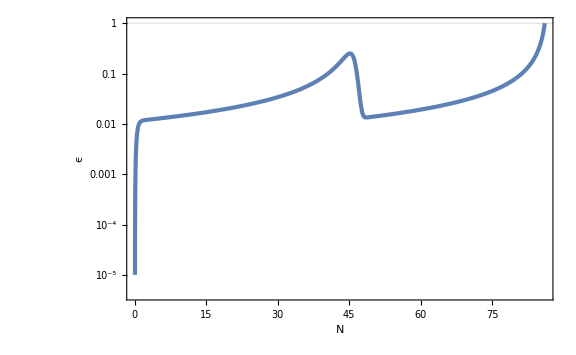

```mathematica
ListLogPlot[eList,FrameLabel->{N,ϵ},GridLines->{None,{1}}]
```

```mathematica
DCptb=Import["double_chaotic_ptb.dat"];
```

```mathematica
phiList=Map[{#[[6]],#[[2]]}&,DCptb];
psiList=Map[{#[[6]],#[[4]]}&,DCptb];
HList=Map[{#[[6]],#[[7]]}&,DCptb];
eList=Map[{#[[6]],#[[8]]}&,DCptb];
```

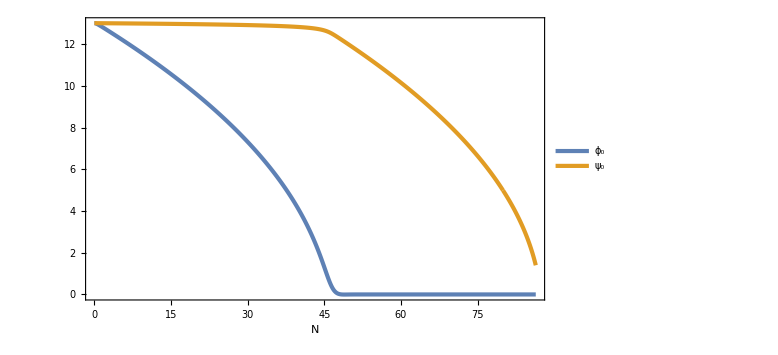

```mathematica
ListPlot[{phiList,psiList},FrameLabel->{N,None},PlotLegends->Placed[{Subscript[ϕ, 0],Subscript[ψ, 0]},{0.2,0.2}]]
```

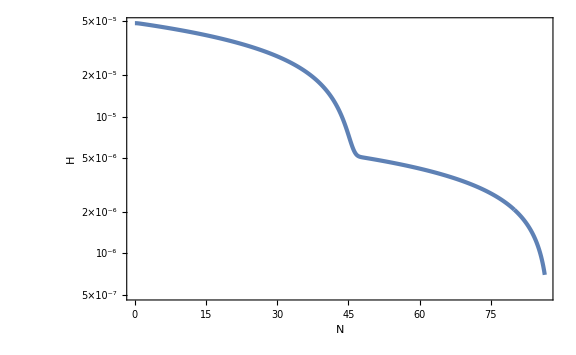

```mathematica
ListLogPlot[HList,FrameLabel->{N,H}]
```

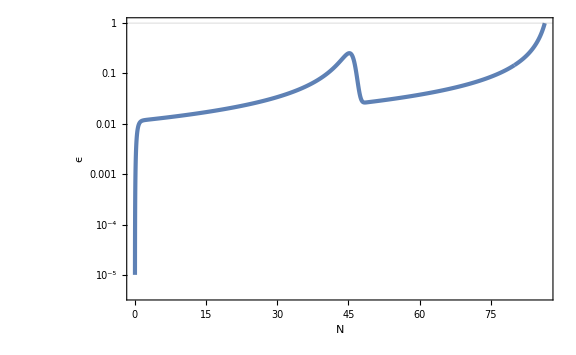

```mathematica
ListLogPlot[eList,FrameLabel->{N,ϵ},GridLines->{None,{1}}]
```